# Kelvin problem (2-d plane strain)

## Integrate point source over 2-d surfaces

```mathematica
x = xo - xs;
y = yo - ys;
C0 = 1/ (4 * Pi *(1-ν));
r = Sqrt[x^2 + y^2];
g = -C0 * Log[r];
gx = -C0*x/r^2;
gy = -C0*y/r^2;
gxy = 2*C0*x*y/r^4;
gxx = C0*(x^2 - y^2)/r^4;
gyy = -gxx;
ux = fx/(2*μ)*((3-4*ν)*g - x*gx) + fy/(2*μ)*(-y*gx) 
uy = fx/(2*μ)*(-x*gy) + fy/(2*μ)*((3-4*ν)*g -y*gy)
sxx = fx*(2*(1 - ν)*gx - x*gxx) + fy*(2*ν* gy - y*gxx);
syy = fx*(2*ν*gx - x*gyy) + fy * (2*(1 - ν)*gy - y*gyy);
sxy = fx*((1 - 2*ν)*gy - x*gxy) + fy*((1 - 2*ν)*gx - y*gxy);
```

-(fy (xo-xs) (-yo+ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fx ((xo-xs)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

-(fx (-xo+xs) (yo-ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fy ((yo-ys)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

```mathematica
uxIndef = Integrate[ReplaceAll[ux,ys->0],xs,GeneratedParameters->C];
uxDef = ReplaceAll[uxIndef,{xs->w}]-ReplaceAll[uxIndef,{xs->-w}]//FullSimplify
uyIndef = Integrate[ReplaceAll[uy,ys->0],xs,GeneratedParameters->C];
uyDef = ReplaceAll[uyIndef,{xs->w}]-ReplaceAll[uyIndef,{xs->-w}]//FullSimplify
```

1/(16 π μ (-1+ν))(16 fx w (-1+ν)-8 fx yo (-1+ν) ArcTan[(w-xo)/yo]-8 fx yo (-1+ν) ArcTan[(w+xo)/yo]+(fy yo-fx (w-xo) (-3+4 ν)) Log[(w-xo)^2+yo^2]-(fy yo+fx (w+xo) (-3+4 ν)) Log[(w+xo)^2+yo^2])

1/(16 π μ (-1+ν))(4 fy w (-3+4 ν)+4 fy yo (-1+2 ν) ArcTan[(-w+xo)/yo]+4 fy yo (1-2 ν) ArcTan[(w+xo)/yo]+(fx yo+fy (-w+xo) (-3+4 ν)) Log[(w-xo)^2+yo^2]-(fx yo+fy (w+xo) (-3+4 ν)) Log[(w+xo)^2+yo^2])

## Surface Integral over some arbitrary shape

```mathematica
vertices={{0,0},{w,0},{0,l}};
(*Step 2:Define the function to integrate*)
f=sxx;
(*Step 3:Define the region of integration*)
region=Triangle[vertices];
(*region = Rectangle[{0,0},{w,w}];*)
(*Step 4:Perform the integration*)
(*uxTri=SurfaceIntegrate[f,{xs,ys}∈region]//FullSimplify*)
uxTri=Integrate[f,{xs,ys}∈region]
```

1/(8 l π w (l^2+w^2)^2 (-1+ν))Abs[l w] (-2 fy l^4 w+2 fx l^3 w^2-2 fy l^2 w^3+2 fx l w^4+4 (l^2+w^2)^2 (fx xo (-1+ν)+fy yo ν) ArcTan[(w-xo)/yo]+4 (l^2+w^2)^2 (fx xo (-1+ν)+fy yo ν) ArcTan[xo/yo]-4 fx l^4 w ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]+4 fy l^3 w^2 ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]-8 fx l^2 w^3 ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]-4 fy l^3 w xo ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]-4 fx w^4 xo ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]+4 fx l^3 w yo ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]-4 fy l^2 w^2 yo ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]+8 fx l w^3 yo ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]+4 fx l^4 w ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]-4 fy l^3 w^2 ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]+4 fx l^2 w^3 ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]-4 fy l w^4 ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]+4 fy l^3 w xo ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]+4 fx l^2 w^2 xo ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]+4 fy l w^3 xo ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]+4 fx w^4 xo ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]-4 fx l^3 w yo ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]+4 fy l^2 w^2 yo ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]-4 fx l w^3 yo ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]+4 fy w^4 yo ν ArcTan[(l^2+w xo-l yo)/(l w-l xo-w yo)]-4 fx l^4 w ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]+4 fy l^3 w^2 ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]-8 fx l^2 w^3 ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]-4 fy l^3 w xo ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]-4 fx w^4 xo ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]+4 fx l^3 w yo ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]-4 fy l^2 w^2 yo ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]+8 fx l w^3 yo ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]+4 fx l^4 w ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]-4 fy l^3 w^2 ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]+4 fx l^2 w^3 ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]-4 fy l w^4 ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]+4 fy l^3 w xo ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]+4 fx l^2 w^2 xo ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]+4 fy l w^3 xo ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]+4 fx w^4 xo ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]-4 fx l^3 w yo ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]+4 fy l^2 w^2 yo ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]-4 fx l w^3 yo ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]+4 fy w^4 yo ν ArcTan[(w^2-w xo+l yo)/(l w-l xo-w yo)]-fy l^4 xo Log[xo^2+yo^2]-2 fy l^2 w^2 xo Log[xo^2+yo^2]-fy w^4 xo Log[xo^2+yo^2]+3 fx l^4 yo Log[xo^2+yo^2]+6 fx l^2 w^2 yo Log[xo^2+yo^2]+3 fx w^4 yo Log[xo^2+yo^2]+2 fy l^4 xo ν Log[xo^2+yo^2]+4 fy l^2 w^2 xo ν Log[xo^2+yo^2]+2 fy w^4 xo ν Log[xo^2+yo^2]-2 fx l^4 yo ν Log[xo^2+yo^2]-4 fx l^2 w^2 yo ν Log[xo^2+yo^2]-2 fx w^4 yo ν Log[xo^2+yo^2]-fy l^4 w Log[w^2-2 w xo+xo^2+yo^2]-fx l^3 w^2 Log[w^2-2 w xo+xo^2+yo^2]+fy l^2 w^3 Log[w^2-2 w xo+xo^2+yo^2]-3 fx l w^4 Log[w^2-2 w xo+xo^2+yo^2]+fy l^4 xo Log[w^2-2 w xo+xo^2+yo^2]+fx l^3 w xo Log[w^2-2 w xo+xo^2+yo^2]-fy l^2 w^2 xo Log[w^2-2 w xo+xo^2+yo^2]+3 fx l w^3 xo Log[w^2-2 w xo+xo^2+yo^2]-3 fx l^4 yo Log[w^2-2 w xo+xo^2+yo^2]+fy l^3 w yo Log[w^2-2 w xo+xo^2+yo^2]-5 fx l^2 w^2 yo Log[w^2-2 w xo+xo^2+yo^2]-fy l w^3 yo Log[w^2-2 w xo+xo^2+yo^2]+2 fy l^4 w ν Log[w^2-2 w xo+xo^2+yo^2]+2 fx l^3 w^2 ν Log[w^2-2 w xo+xo^2+yo^2]+2 fy l^2 w^3 ν Log[w^2-2 w xo+xo^2+yo^2]+2 fx l w^4 ν Log[w^2-2 w xo+xo^2+yo^2]-2 fy l^4 xo ν Log[w^2-2 w xo+xo^2+yo^2]-2 fx l^3 w xo ν Log[w^2-2 w xo+xo^2+yo^2]-2 fy l^2 w^2 xo ν Log[w^2-2 w xo+xo^2+yo^2]-2 fx l w^3 xo ν Log[w^2-2 w xo+xo^2+yo^2]+2 fx l^4 yo ν Log[w^2-2 w xo+xo^2+yo^2]-2 fy l^3 w yo ν Log[w^2-2 w xo+xo^2+yo^2]+2 fx l^2 w^2 yo ν Log[w^2-2 w xo+xo^2+yo^2]-2 fy l w^3 yo ν Log[w^2-2 w xo+xo^2+yo^2]+fy l^4 w Log[l^2+xo^2-2 l yo+yo^2]+fx l^3 w^2 Log[l^2+xo^2-2 l yo+yo^2]-fy l^2 w^3 Log[l^2+xo^2-2 l yo+yo^2]+3 fx l w^4 Log[l^2+xo^2-2 l yo+yo^2]-fx l^3 w xo Log[l^2+xo^2-2 l yo+yo^2]+3 fy l^2 w^2 xo Log[l^2+xo^2-2 l yo+yo^2]-3 fx l w^3 xo Log[l^2+xo^2-2 l yo+yo^2]+fy w^4 xo Log[l^2+xo^2-2 l yo+yo^2]-fy l^3 w yo Log[l^2+xo^2-2 l yo+yo^2]-fx l^2 w^2 yo Log[l^2+xo^2-2 l yo+yo^2]+fy l w^3 yo Log[l^2+xo^2-2 l yo+yo^2]-3 fx w^4 yo Log[l^2+xo^2-2 l yo+yo^2]-2 fy l^4 w ν Log[l^2+xo^2-2 l yo+yo^2]-2 fx l^3 w^2 ν Log[l^2+xo^2-2 l yo+yo^2]-2 fy l^2 w^3 ν Log[l^2+xo^2-2 l yo+yo^2]-2 fx l w^4 ν Log[l^2+xo^2-2 l yo+yo^2]+2 fx l^3 w xo ν Log[l^2+xo^2-2 l yo+yo^2]-2 fy l^2 w^2 xo ν Log[l^2+xo^2-2 l yo+yo^2]+2 fx l w^3 xo ν Log[l^2+xo^2-2 l yo+yo^2]-2 fy w^4 xo ν Log[l^2+xo^2-2 l yo+yo^2]+2 fy l^3 w yo ν Log[l^2+xo^2-2 l yo+yo^2]+2 fx l^2 w^2 yo ν Log[l^2+xo^2-2 l yo+yo^2]+2 fy l w^3 yo ν Log[l^2+xo^2-2 l yo+yo^2]+2 fx w^4 yo ν Log[l^2+xo^2-2 l yo+yo^2])

```mathematica
TimeConstrained[Collect[uxTri,{fx,fy,μ(-1+ν)},FullSimplify],30]
```

$Aborted

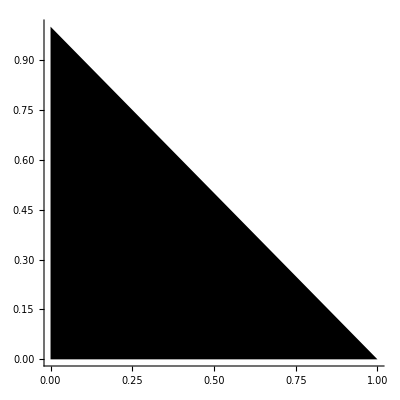

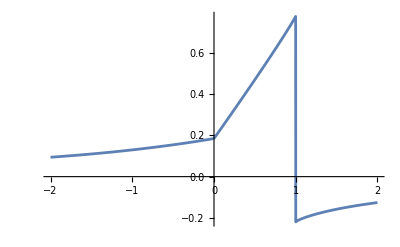

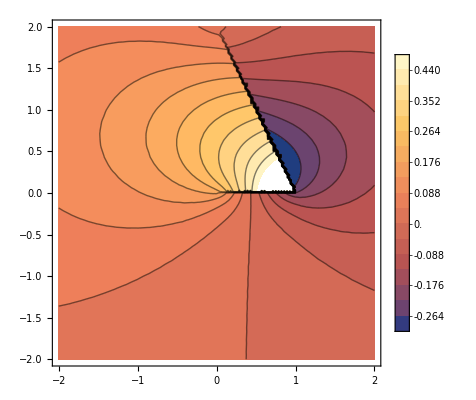

```mathematica
Graphics[{ReplaceAll[region,{w->1,l->1,q->0.5}]},Axes->True]
Plot[ReplaceAll[uxTri,{fx->1,fy->0,μ->1,ν->0.25,w->1,l->2,q->0.5,yo->0.001}],{xo,-2,2}]
ContourPlot[ReplaceAll[uxTri,{fx->1,fy->0,μ->1,ν->0.25,w->1,l->2,q->0.5}],{xo,-2,2},{yo,-2,2},PlotLegends->Automatic,Contours->21]
```